```mathematica
wd=NotebookDirectory[];
appPath="+mem="<>wd<>"dhrystone.bin";
```

```mathematica
LibraryUnload[libhello]
```

```mathematica
<<"/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/math.m"
```

```mathematica
pclist = Table[nextpc[],10000];
```

```mathematica
g=Union[BlockMap[#[[1]]->#[[2]]&,pclist,2,1]];
```

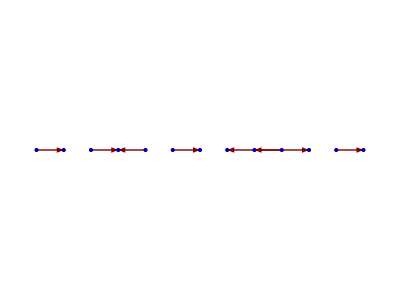

```mathematica
GraphPlot[Select[g,(#[[2]]-#[[1]])>100&],DirectedEdges-> True,Method->"LinearEmbedding"]
```

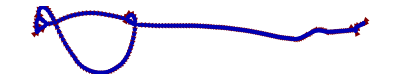

```mathematica
GraphPlot[g,DirectedEdges-> True]
```

```mathematica
Dataset[Table[{i,BaseForm[getregister[i],16],BaseForm[getregister[i],2]},{i,1,31}]]
```

Dataset[<>]

```mathematica
reset["+mem=/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/dhrystone.bin"];
```

```mathematica
regs=Table[{i,getregister[i]},{i,1,31}];
```

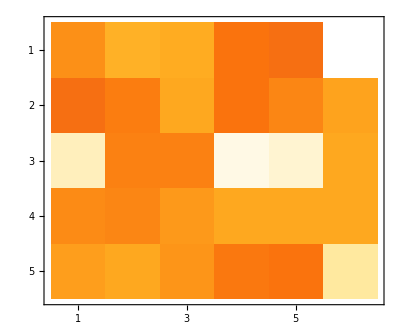

```mathematica
MatrixPlot[BlockMap[#&,Map[#[[2]]&,regs],6],ColorFunction->"SunsetColors"]
```

```mathematica
Table[nextpc[],10000];
```

```mathematica
ListAnimate[Table[nextpc[];MatrixPlot[BlockMap[#&,Map[#[[2]]&,Table[{i,getregister[i]},{i,1,31}]],6],ColorFunction->"SunsetColors"],
1000
]]
```

```mathematica
reglist[]
```

{0,2768,65344,13600,0,-1,1498564676,-1,3,12288,0,67,11648,1230132307,66,66,1380982853,1313821779,12288,500,67,9996,12288,12288,12288,11636,12288,9964,2,0,1095911247}

```mathematica
branchstate[]
```

{512,0,0,0,0}

```mathematica
branchstatelist=Table[nextpc[];branchstate[],20000];
```

```mathematica
Export["branchstatelist.xml",branchstatelist]
```

branchstatelist.xml

```mathematica
readmem[512,100]
```

{151,49,0,0,147,129,1,50,151,53,0,0,147,133,133,179,23,86,0,0,19,6,6,59,33,160,35,160,5,0,145,5,227,157,197,254,23,1,1,0,19,1,193,221,183,2,73,0,5,67,35,160,98,0,183,2,73,0,147,130,66,0,19,3,48,6,35,160,98,0,183,2,73,0,147,130,2,1,125,83,35,160,98,0,35,162,98,0,1,69,129,69,239,0,192,98,111,16,16,50}

{}

```mathematica
pclog={};
While[!isFinished[],
pclog=Append[pclog,nextpc[]]
]
```

```mathematica
Length[pclog]
```

197598

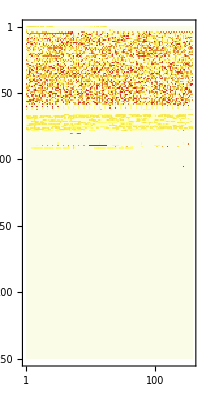

```mathematica
MatrixPlot[BlockMap[#&,Map[#&,readmem[0,32000]],128],ColorFunction->"TemperatureMap"]
```

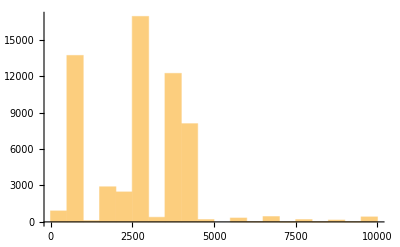

```mathematica
Histogram[Select[memaddr,#>0 && #<10000&]]
```

```mathematica
bus=Table[step[];readdatabus[],10]
```

{{2,1},{2878,1},{2894,1},{2894,1},{11616,2},{2897,2},{2892,2},{2892,2},{11628,2},{2899,2}}

```mathematica
readmem[0,10]
```

{69,120,101,99,117,116,105,111,110,32}

```mathematica
busclaen=Select[bus,#[[1]]>0 &];
```

```mathematica
busdatamul=Flatten[Map[
Range[
#[[1]],#[[1]]+(#[[2]]-1)
]&,
busclaen]];
```

```mathematica
stat=Tally[busdatamul]
```

{{12800,2},{1316,1},{12808,2},{21008,2},{1476,1},{544,1},{538,7777},{11584,1},{11585,1},{546,2592},{547,2592},{539,7774},{11588,1},{11589,1},{11592,1},{11593,1},{11596,1},{11597,1},{11600,2},{11601,2},6120,{3874,376},{2768,752},{2746,1128},{2747,1128},{2751,376},{3007,376},{2858,564},{2859,188},{2862,376},{2935,6006},{2878,187},{2894,374},{2897,187},{2898,187},{2892,374},{2893,374},{2899,374},{2900,374},{2604,187},{2605,187}}
 |  |  |  |

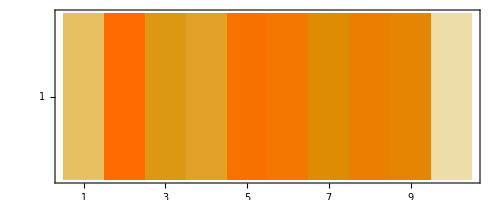

```mathematica
MatrixPlot[BlockMap[#&,Map[#&,readmem[0,10]],10],ColorRules->{}]
```

```mathematica
BlockMap[#&,stat,10]
```

{{{12800,2},{1316,1},{12808,2},{21008,2},{1476,1},{544,1},{538,7777},{11584,1},{11585,1},{546,2592}},{{547,2592},{539,7774},{11588,1},{11589,1},{11592,1},{11593,1},{11596,1},{11597,1},{11600,2},{11601,2}},613,{{2878,187},{2894,374},{2897,187},{2898,187},{2892,374},{2893,374},{2899,374},{2900,374},{2604,187},{2605,187}}}
 |  |  |  |

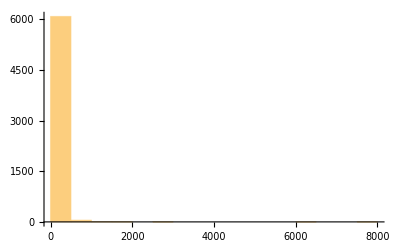

```mathematica
Histogram[stat[[All,2]]]
```